```mathematica
$Assumptions=θ∈Reals&&0≤θ≤π;
```

```mathematica
ωA=ArcSin[(2*Cos[θ]*(Sqrt[2]-Sin[θ]))/(3+Cos[2*θ])];
ωB=ArcSin[(2*Cos[θ]*(Sqrt[2]+Sin[θ]))/(3+Cos[2*θ])];
```

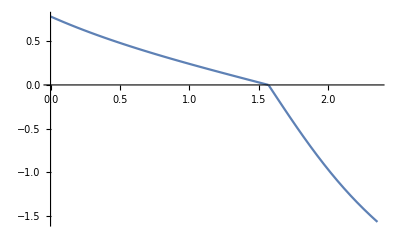

```mathematica
Plot[If[θ≤π/2,ωA,ωB],{θ,0,3*π/4}]
```

```mathematica
ω[θArg_]:=If[θArg≤π/2,ωA/.{θ->θArg},ωB/.{θ->θArg}]
```

```mathematica
ω[0]
```

π/4

```mathematica
FullSimplify[ω[3*π/4]]
```

-π/2

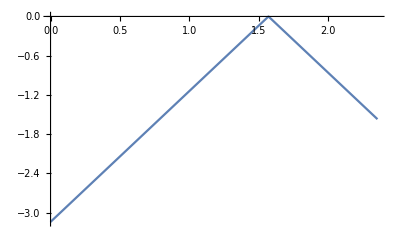

```mathematica
γm[θ_]:=-Abs[2*θ-π];
Plot[γm[θ],{θ,0,3*π/4}]
```

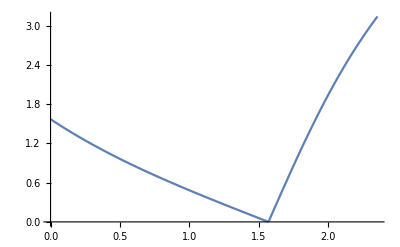

```mathematica
γv[θ_]:=If[θ≤π/2,2 (ArcCsc[√(1+Cos[θ]^2)]-ArcCsc[√(1+Cos[θ]^2) Csc[θ]]),2 (ArcCos[Sin[θ]/(√(1+Cos[θ]^2))]+ArcSec[√(1+Cos[θ]^2)])];
Plot[γv[θ],{θ,0,3*π/4}]
```

```mathematica
reflIf[θ_,flag_]:=If[flag,π-θ,θ]
```

```mathematica
U[kmVec_,kvVec_,θ0mVec_,θ0vVec_,reflFlags_,θ_]:=Sum[kmVec[[i]]/2*(γm[reflIf[θ,reflFlags[[i]]]]-γm[θ0mVec[[i]]])^2+kvVec[[i]]/2*(γv[reflIf[θ,reflFlags[[i]]]]-γv[θ0vVec[[i]]])^2,{i,1,Length[kmVec]}]
```

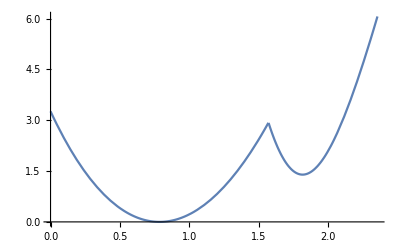

```mathematica
Plot[U[{2},{2},{π/4},{π/4},{False},θ],{θ,0,3*π/4}]
```

```mathematica
Manipulate[Plot[U[{km1,km2},{kv1,kv2},{θ0m1,θ0m2},{θ0v1,θ0v2},{False,rf2},θ],{θ,0,π},PlotRange->{0,Automatic}],{{km1,1},0,5,0.5},{{km2,1},0,5,0.5},{{kv1,1},0,5,0.5},{{kv2,1},0,5,0.5},{{θ0m1,π/4},0,π/2,π/24},{{θ0m2,π/4},0,π/2,π/24},{{θ0v1,π/4},0,π/2,π/24},{{θ0v2,π/4},0,π/2,π/24},{rf2,{False,True}}]
```

```mathematica
Manipulate[Plot[{U[{km1,km2},{kv1,kv2},{θ0m1,θ0m2},{θ0v1,θ0v2},{False,False},θ],U[{km1,km2},{kv1,kv2},{θ0m1,θ0m2},{θ0v1,θ0v2},{False,True},θ]},{θ,0,π},PlotRange->{0,Automatic},PlotLegends->Automatic],{{km1,1},0,5,0.5},{{km2,1},0,5,0.5},{{kv1,1},0,5,0.5},{{kv2,1},0,5,0.5},{{θ0m1,π/4},0,π/2,π/24},{{θ0m2,π/4},0,π/2,π/24},{{θ0v1,π/4},0,π/2,π/24},{{θ0v2,π/4},0,π/2,π/24}]
```

```mathematica
Manipulate[Plot[U[{km1,km2,km3},{kv1,kv2,kv3},{θ0m1,θ0m2,θ0m3},{θ0v1,θ0v2,θ0m3},{False,rf2,rf3},θ],{θ,0,π},PlotRange->{0,Automatic}],{{km1,1},0,5,0.5},{{km2,1},0,5,0.5},{{km3,1},0,5,0.5},{{kv1,1},0,5,0.5},{{kv2,1},0,5,0.5},{{kv3,1},0,5,0.5},{{θ0m1,π/4},0,π/2,π/24},{{θ0m2,π/4},0,π/2,π/24},{{θ0m3,π/4},0,π/2,π/24},{{θ0v1,π/4},0,π/2,π/24},{{θ0v2,π/4},0,π/2,π/24},{{θ0v2,π/4},0,π/2,π/24},{rf2,{False,True}},{rf3,{False,True}}]
```

```mathematica
Manipulate[ListPlot[Table[{(NN-n)*ω[θ]+n*ω[π-θ],Factorial[NN]/(Factorial[NN-n]*Factorial[n])},{n,0,NN}]],{{θ,π/4},0,3*π/4,π/32},{{NN,5},1,25}]
```

```mathematica
Clear[θ]
```

```mathematica
ConfigsTable[NN_,θ_]:=Table[{(NN-n)*ω[θ]+n*ω[π-θ],(Factorial[NN]/(Factorial[NN-n]*Factorial[n]))},{n,0,NN}];
```

```mathematica
p=Manipulate[ListPlot[{ConfigsTable[NN,π/4],ConfigsTable[NN,3*π/8],ConfigsTable[NN,7*π/16],ConfigsTable[NN,π/2]},PlotMarkers->Automatic,PlotLegends->{"θ=π/4","θ=3*π/8","θ=7π/16","θ=π/2"}],{{NN,5},1,25}]
```

```mathematica
Export["~/google-drive/Temp/2020-07-14/omega-vs-nconfigs_N-14.png",ListPlot[{ConfigsTable[14,π/4],ConfigsTable[14,3*π/8],ConfigsTable[14,7*π/16],ConfigsTable[14,π/2]},PlotMarkers->Automatic,PlotLegends->{"θ=π/4","θ=3π/8","θ=7π/16","θ=π/2"},AxesLabel->{Ω,NΩ}]
]
```

Export::nodir: Directory C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-14\ does not exist.

Export::noopen: Cannot open ~/google-drive/Temp/2020-07-14/omega-vs-nconfigs_N-14.png.

$Failed

```mathematica
UExprA=Simplify[1/2*(γv[θ]-γv0)^2,0≤θ<π/2]
```

1/2 (γv0-2 ArcCsc[√(1+Cos[θ]^2)]+2 ArcCsc[√(1+Cos[θ]^2) Csc[θ]])^2

```mathematica
dUExprA=FullSimplify[D[UExprA,{θ,2}],0≤θ<π/2]
```

(4 (-2+(γv0-2 ArcCsc[√(1+Cos[θ]^2)]+2 ArcCsc[√(1+Cos[θ]^2) Csc[θ]]) Cos[θ]) (-5+Cos[2 θ]+4 √2 Sin[θ]))/(3+Cos[2 θ])^2

```mathematica
NMinimize[{dUExprA/.{γv0->π/4},0≤θ<π/2},{θ}][[1]]
```

0.653947

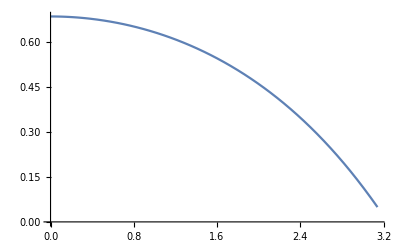

```mathematica
Plot[NMinimize[{dUExprA/.{γv0->γvv},0≤θ<π/2},{θ}][[1]],{γvv,0,π}]
```

```mathematica
(*Export["~/Dev/origami-paper-1/PRL/figs/convexA.csv",Table[{N[γvv],NMinimize[{dUExprA/.{γv0->γvv},0≤θ<π/2},{θ}][[1]]},{γvv,0,3*π/2,π/24}]]*)
```

```mathematica
UExprB=Simplify[1/2*(γv[θ]-γv0)^2,π/2<θ≤3*π/4]
```

1/2 (γv0-2 (ArcCos[Sin[θ]/(√(1+Cos[θ]^2))]+ArcSec[√(1+Cos[θ]^2)]))^2

```mathematica
dUExprB=Simplify[D[UExprB,{θ,2}],π/2<θ≤3*π/4]
```

(4 (-2+γv0 Cos[θ]-2 ArcCos[Sin[θ]/(√(1+Cos[θ]^2))] Cos[θ]-2 ArcSec[√(1+Cos[θ]^2)] Cos[θ]) (-5+Cos[2 θ]-4 √2 Sin[θ]))/(3+Cos[2 θ])^2

```mathematica
(*Export["~/Dev/origami-paper-1/PRL/figs/convexB.csv",Table[{N[γvv],NMinimize[{dUExprB/.{γv0->γvv},π/2<θ≤3*π/4},{θ}][[1]]},{γvv,0,3*π/2,π/24}]]*)
```

```mathematica
solveA=Solve[dUExprA==0,γv0]
```

{{γv0→2 (ArcCsc[√(1+Cos[θ]^2)]-ArcCsc[√(1+Cos[θ]^2) Csc[θ]]+Sec[θ])}}

## Visualization

## single unit

```mathematica
refTri={{0,0,0},{1,0,0},{1,1,0}};
rvec=Array[r,3];
A[r_]:={{0,-r[[3]],r[[2]]},{r[[3]],0,-r[[1]]},{-r[[2]],r[[1]],0}};
```

```mathematica
A[rvec]+Transpose[A[rvec]]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Q[rvec_,θ_]:=(1-Cos[θ])*rvec⊗rvec+Cos[θ]*IdentityMatrix[3]+Sin[θ]*A[rvec]
FullSimplify[Q[rvec,θ].Transpose[Q[rvec,θ]],rvec.rvec==1]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
rotate[points_,u_,θ_]:=Transpose[Q[u,θ].Transpose[points]];
```

```mathematica
transX[points_,c_]:=Module[{x=points},
For[i=1,i≤Length[x],i++,
x[[i]]=x[[i]]+c;
];
x
]
```

```mathematica
θToψ={θ->π/2-ψ};
ψToθ={ψ->π/2-θ};
rm={0,1,0}
r1={1/Sqrt[2],-1/Sqrt[2],0}
rm1=Simplify[Q[r1,ψ].rm]
```

{0,1,0}

{1/(√2),-1/(√2),0}

{1/2 (-1+Cos[ψ]),Cos[ψ/2]^2,Sin[ψ]/(√2)}

```mathematica
θv=θ/.θToψ
r2=Simplify[{-Sin[θv]/Sqrt[2],-Sin[θv]/Sqrt[2],-Cos[θv]}]
```

π/2-ψ

{-Cos[ψ]/(√2),-Cos[ψ]/(√2),-Sin[ψ]}

```mathematica
rm2=FullSimplify[Q[r2,ϕ1].rm1]
```

{1/2 (-Cos[ϕ1]+Cos[ψ]+Sin[ϕ1] Sin[ψ]),1/2 (Cos[ϕ1]+Cos[ψ]+Sin[ϕ1] Sin[ψ]),(-Cos[ψ] Sin[ϕ1]+Sin[ψ])/(√2)}

```mathematica
θϕToTri[θ_,ϕ_]:=Transpose[Q[r2/.{ψ->π/2-θ},ϕ].Q[r1,π/2-θ].Transpose[refTri]]
```

```mathematica
θϕToRm[θ_,ϕ_]:=Module[{tri,rmv},
tri=θϕToTri[θ,ϕ];
rmv=tri[[3]]-tri[[2]];
rmv
]
```

```mathematica
compat=Simplify[Solve[(θϕToRm[θ,ϕ1])[[1]]==0,{ϕ1}]]/.{C[1]->0}
```

{{ϕ1→ArcTan[-√2 Cos[θ]^2+Sin[θ],-Cos[θ] (√2+Sin[θ])]},{ϕ1→ArcTan[√2 Cos[θ]^2+Sin[θ],Cos[θ] (√2-Sin[θ])]}}

```mathematica
reflXY[points_]:=Module[{x=points,temp},
For[i=1,i≤Length[x],i++,
temp=x[[i]][[1]];
x[[i]][[1]]=x[[i]][[2]];
x[[i]][[2]]=temp;
];
x
];
reflX[points_,idx_]:=Module[{x=points},
For[i=1,i≤Length[x],i++,
x[[i]][[idx]]=-x[[i]][[idx]];
];
x
];
```

```mathematica
θϕToTri2[θ_,ϕ_]:=Transpose[Q[-r2/.{ψ->π/2-θ},ϕ].Q[r1,π/2-θ].Transpose[reflXY[refTri]]]
```

```mathematica
θϕToTri2[π/2,0]
```

{{0,0,0},{0,1,0},{1,1,0}}

```mathematica
refl1[points_,θ_]:=transX[reflX[transX[points,{-Sin[θ],0,0}],1],{Sin[θ],0,0}];
refl2[points_,θ_]:=transX[reflX[transX[points,{0,-Sin[θ],0}],2],{0,Sin[θ],0}];
```

```mathematica
Manipulate[
ϕ1vv=(ϕ1/.compat[[ϕ1Idx]])/.{θ->θvv};
ϕ2vv=(ϕ1/.compat[[ϕ2Idx]])/.{θ->θvv};
aTri1=θϕToTri[θvv,ϕ1vv];
aTri2=θϕToTri2[θvv,ϕ2vv];
aTri3=refl1[aTri1,θvv];
aTri4=refl1[aTri2,θvv];
aTri5=refl2[aTri1,θvv];
aTri6=refl2[aTri2,θvv];
aTri7=refl2[aTri3,θvv];
aTri8=refl2[aTri4,θvv];
Graphics3D[{Triangle[aTri1],Triangle[aTri2],Triangle[aTri3],Triangle[aTri4],Triangle[aTri5],Triangle[aTri6],Triangle[aTri7],Triangle[aTri8]},Boxed->False],
{{θvv,π/12},0,3*π/4,π/24},{{ϕ1Idx,1},{1,2}},{{ϕ2Idx,1},{1,2}}
]
```

```mathematica
Clear[Waterbomb]
```

```mathematica
Waterbomb[θv_,ϕ1Idx_,ϕ2Idx_]:=Module[{aTri1,aTri2,aTri3,aTri4,aTri5,aTri6,aTri7,aTri8,ϕ1v,ϕ2v,tris,k},
ϕ1v=(ϕ1/.compat[[ϕ1Idx]])/.{θ->θv};
ϕ2v=(ϕ1/.compat[[ϕ2Idx]])/.{θ->θv};
aTri1=θϕToTri[θv,ϕ1v];
aTri2=θϕToTri2[θv,ϕ2v];
aTri3=refl1[aTri1,θv];
aTri4=refl1[aTri2,θv];
aTri5=refl2[aTri1,θv];
aTri6=refl2[aTri2,θv];
aTri7=refl2[aTri3,θv];
aTri8=refl2[aTri4,θv];
tris={aTri1,aTri2,aTri3,aTri4,aTri5,aTri6,aTri7,aTri8};
{
Catenate[{{EdgeForm[]},Table[Triangle[tri],{tri, tris}]}],
Catenate[{{EdgeForm[{Black}]},Catenate[Table[
If[k==5||k==1||k==3||k==7,
{Line[{tris[[k]][[1]],tris[[k]][[3]]}],Line[{tris[[k]][[2]],tris[[k]][[3]]}],Line[{tris[[k]][[1]],tris[[k]][[2]]}]},
{Line[{tris[[k]][[1]],tris[[k]][[3]]}],Line[{tris[[k]][[2]],tris[[k]][[3]]}]}
]
,{k,1,Length[tris]}]]}]
}
];
```

```mathematica
θToCompat[θ_]:=If[θ≤π/2,2,1]
```

```mathematica
(*Export["symm-folding.gif",Manipulate[Graphics3D[Waterbomb[θv,If[θv≤π/2,2,1],If[θv≤π/2,2,1]],Boxed->False],{{θv,0},0,3*π/4,π/128}]]*)
```

```mathematica
WaterbombStrip[θv_,switches_]:=Module[{WBs,θi,WBi,i,j,ci,ui,ωi,uhati,Σω,WB1Tris,WBNTris,WB1u,WB1v,WBNu,WBNv,WB1n,WBNn},
Σω=ω[θv];
WBs={Waterbomb[θv,θToCompat[θv],θToCompat[θv]]};
For[i=2,i≤Length[switches],i++,
θi=If[switches[[i]],θv,π-θv];
WBi=Waterbomb[θi,θToCompat[θi],θToCompat[θi]];
ci=WBs[[i-1]][[1]][[4+1]][[1]][[1]]-WBi[[1]][[2+1]][[1]][[1]];
ui=WBs[[i-1]][[1]][[8+1]][[1]][[1]]-WBs[[i-1]][[1]][[4+1]][[1]][[1]];
uhati=ui/Sqrt[ui.ui];
Σω=Σω+ω[θi];
For[j=2,j≤Length[WBi[[1]]],j++,
WBi[[1]][[j]][[1]]=transX[rotate[WBi[[1]][[j]][[1]],uhati,Σω],ci];
];
For[j=2,j≤Length[WBi[[2]]],j++,
WBi[[2]][[j]][[1]]=transX[rotate[WBi[[2]][[j]][[1]],uhati,Σω],ci];
];
Σω=Σω+ω[θi];
AppendTo[WBs,WBi];
];
WB1Tris=WBs[[1]][[1]];
WBNTris=Last[WBs][[1]];
WB1u=WB1Tris[[7]][[1]][[2]]-WB1Tris[[7]][[1]][[1]];
WB1v=WB1Tris[[3]][[1]][[2]]-WB1Tris[[3]][[1]][[1]];
WB1n=WB1u×WB1v;
WBNu=WBNTris[[5]][[1]][[2]]-WBNTris[[5]][[1]][[1]];
WBNv=WBNTris[[9]][[1]][[2]]-WBNTris[[9]][[1]][[1]];
WBNn=WBNu×WBNv;
{WBs,{EdgeForm[Black],Line[{WB1Tris[[3]][[1]][[1]],WB1Tris[[3]][[1]][[2]]}],Line[{WB1Tris[[7]][[1]][[1]],WB1Tris[[7]][[1]][[2]]}],Line[{WBNTris[[5]][[1]][[1]],WBNTris[[5]][[1]][[2]]}],Line[{WBNTris[[9]][[1]][[1]],WBNTris[[9]][[1]][[2]]}]},
{EdgeForm[Black],Arrow[{WB1Tris[[3]][[1]][[2]],WB1Tris[[3]][[1]][[2]]-WB1n}],Arrow[{WBNTris[[5]][[1]][[2]],WBNTris[[5]][[1]][[2]]+WBNn}]},
{Opacity[0.5],Polygon[rotate[{{0,2.0,1.5},{0,2.0,-0.5},{0,-0.5,-0.5},{0,-0.5,1.5}},{0,1,0},-ω[θv]]]},
{Opacity[0.5],Polygon[transX[rotate[{{0,2.0,1.5},{0,2.0,-0.5},{0,-0.5,-0.5},{0,-0.5,1.5}},{0,1,0},Σω],WBNTris[[5]][[1]][[1]]]]}
}
]
WaterbombStripPlanes[θv_,switches_]:=Module[{WBs,θi,WBi,i,j,ci,ui,ωi,uhati,Σω,WB1Tris,WBNTris,WB1u,WB1v,WBNu,WBNv,WB1n,WBNn},
Σω=ω[θv];
WBs={Waterbomb[θv,θToCompat[θv],θToCompat[θv]]};
For[i=2,i≤Length[switches],i++,
θi=If[switches[[i]],θv,π-θv];
WBi=Waterbomb[θi,θToCompat[θi],θToCompat[θi]];
ci=WBs[[i-1]][[1]][[4+1]][[1]][[1]]-WBi[[1]][[2+1]][[1]][[1]];
ui=WBs[[i-1]][[1]][[8+1]][[1]][[1]]-WBs[[i-1]][[1]][[4+1]][[1]][[1]];
uhati=ui/Sqrt[ui.ui];
Σω=Σω+ω[θi];
For[j=2,j≤Length[WBi[[1]]],j++,
WBi[[1]][[j]][[1]]=transX[rotate[WBi[[1]][[j]][[1]],uhati,Σω],ci];
];
For[j=2,j≤Length[WBi[[2]]],j++,
WBi[[2]][[j]][[1]]=transX[rotate[WBi[[2]][[j]][[1]],uhati,Σω],ci];
];
Σω=Σω+ω[θi];
AppendTo[WBs,WBi];
];
WB1Tris=WBs[[1]][[1]];
WBNTris=Last[WBs][[1]];
WB1u=WB1Tris[[7]][[1]][[2]]-WB1Tris[[7]][[1]][[1]];
WB1v=WB1Tris[[3]][[1]][[2]]-WB1Tris[[3]][[1]][[1]];
WB1n=WB1u×WB1v;
WBNu=WBNTris[[5]][[1]][[2]]-WBNTris[[5]][[1]][[1]];
WBNv=WBNTris[[9]][[1]][[2]]-WBNTris[[9]][[1]][[1]];
WBNn=WBNu×WBNv;
{
{EdgeForm[Black],Arrow[{{0,0,0},-WB1n}],Arrow[{{0,0,0},WBNn}]},
{Opacity[0.5],Polygon[rotate[{{0.0,-1.0,1.0},{0.0,-1.0,-1.0},{0.0,1.0,-1.0},{0.0,1.0,1.0}},{0,1,0},-ω[θv]]]},
{Opacity[0.5],Polygon[rotate[{{0.0,-1.0,1.0},{0.0,-1.0,-1.0},{0.0,1.0,-1.0},{0.0,1.0,1.0}},{0,1,0},Σω]]}
}
]
```

```mathematica
Graphics3D[WaterbombStrip[3*π/8,{True,True,False,True,False}],Boxed->False,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Graphics3D[WaterbombStripPlanes[π/3,{True,True,False,True}],Boxed->False,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Graphics3D[WaterbombStrip[π/3+π/24,{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}],Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[WaterbombStrip[7*π/12,{True,True}],Boxed->False]
```

-Graphics3D-

```mathematica
(*Export["up-down_to_down-up.gif",Animate[Graphics3D[WaterbombStrip[θv,{True,False}],Boxed->False],{θv,π/4,3*π/4,π/64},AnimationRepetitions->Infinity,AnimationRunning->True]]*)
```

```mathematica
(*Export["up-down_to_down-up_energy.gif",Animate[Show[Plot[U[{Sqrt[2],Sqrt[2]},{1,1},{π/4,π/4},{π/4,π/4},{True,False},θ],{θ,π/4,3*π/4},PlotRange->{0,Automatic}],ListPlot[{{θv,U[{Sqrt[2],Sqrt[2]},{1,1},{π/4,π/4},{π/4,π/4},{True,False},θv]}}]],{{θv,π/4},π/4,3*π/4,π/64},AnimationRepetitions->Infinity,AnimationRunning->True]]*)
```

```mathematica
(*Animate[Graphics3D[WaterbombStrip[θv,{True,False}],Boxed->False];Plot[U[{Sqrt[2],Sqrt[2]},{1,1},{π/4,π/4},{π/4,π/4},{True,False},θ],{θ,π/4,3*π/4},PlotRange->{0,Automatic}],{θv,π/4,3*π/4,π/64},AnimationRepetitions->Infinity,AnimationRunning->False]*)
```

```mathematica
Graphics3D[WaterbombStrip[5*π/8+π/64+π/128,{True,True,True}],Boxed->False]
```

-Graphics3D-

```mathematica
WaterbombStripIncompat[θv_,switches_]:=Module[{WBs,θi,WBi,i,j,ci,ui,ωi,uhati},
WBs={Waterbomb[θv,θToCompat[θv],θToCompat[θv]]};
For[i=2,i≤Length[switches],i++,
θi=If[switches[[i]],θv,π-θv];
WBi=Waterbomb[θi,θToCompat[θi],θToCompat[θi]];
ci=WBs[[i-1]][[4]][[1]][[1]]-WBi[[2]][[1]][[1]];
ui=WBs[[i-1]][[8]][[1]][[1]]-WBs[[i-1]][[4]][[1]][[1]];
uhati=ui/Sqrt[ui.ui];
For[j=1,j≤Length[WBi],j++,
WBi[[j]][[1]]=transX[WBi[[j]][[1]],ci];
];
AppendTo[WBs,WBi];
];
WBs
]
```

```mathematica
Graphics3D[WaterbombStripIncompat[π/3,{True,False}],Boxed->False,ViewPoint->Front]
```

Part::partw: Part 4 of … does not exist.

Thread::tdlen: Objects of unequal length in … cannot be combined.

Part::partw: Part 8 of … does not exist.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

-Graphics3D-

```mathematica
Manipulate[Graphics3D[WaterbombStrip[θ,{True,switch1,switch2,switch3,switch4}],Boxed->False],{{θ,π/2},0,3*π/4,π/128},{switch1,{True,False}},{switch2,{True,False}},{switch3,{True,False}},{switch4,{True,False}}]
```

```mathematica
reflWaterbomb[wb_]:=Module[{newWb,i},
newWb={};
For[i=1,i≤Length[wb],i++,
AppendTo[newWb,Triangle[reflX[wb[[i]][[1]],1]]];
];
newWb
];
rotWaterbomb[wb_,uhat_,ω_]:=Module[{newWb,i},
newWb={};
For[i=1,i≤Length[wb],i++,
AppendTo[newWb,Triangle[rotate[wb[[i]][[1]],uhat,ω]]];
];
newWb
];
```

```mathematica
wb=Waterbomb[π/2,1,1]
```

{{EdgeForm[],Triangle[{{0,0,0},{1,0,0},{1,1,0}}],Triangle[{{0,0,0},{0,1,0},{1,1,0}}],Triangle[{{2,0,0},{1,0,0},{1,1,0}}],Triangle[{{2,0,0},{2,1,0},{1,1,0}}],Triangle[{{0,2,0},{1,2,0},{1,1,0}}],Triangle[{{0,2,0},{0,1,0},{1,1,0}}],Triangle[{{2,2,0},{1,2,0},{1,1,0}}],Triangle[{{2,2,0},{2,1,0},{1,1,0}}]},{EdgeForm[{GrayLevel[0]}],Line[{{0,0,0},{1,1,0}}],Line[{{1,0,0},{1,1,0}}],Line[{{0,0,0},{1,0,0}}],Line[{{0,0,0},{1,1,0}}],Line[{{0,1,0},{1,1,0}}],Line[{{2,0,0},{1,1,0}}],Line[{{1,0,0},{1,1,0}}],Line[{{2,0,0},{1,0,0}}],Line[{{2,0,0},{1,1,0}}],Line[{{2,1,0},{1,1,0}}],Line[{{0,2,0},{1,1,0}}],Line[{{1,2,0},{1,1,0}}],Line[{{0,2,0},{1,2,0}}],Line[{{0,2,0},{1,1,0}}],Line[{{0,1,0},{1,1,0}}],Line[{{2,2,0},{1,1,0}}],Line[{{1,2,0},{1,1,0}}],Line[{{2,2,0},{1,2,0}}],Line[{{2,2,0},{1,1,0}}],Line[{{2,1,0},{1,1,0}}]}}

```mathematica
reflWaterbomb[wb]
```

{Triangle[EdgeForm[]],Triangle[EdgeForm[{-GrayLevel[0]}]]}

```mathematica
Length[WaterbombStrip[π/2,{True,True,True}]]
```

5

```mathematica
(*Manipulate[Graphics3D[rotWaterbomb[Waterbomb[θ,1,1],{0,1,0},ω[θ]]],{{θ,π/2},0,3*π/4,π/64}]*)
```

```mathematica
(*Manipulate[
WBStripTemp=WaterbombStrip[θ,{True,switch1,switch2,switch3,switch4}];
WBStrip1={};
For[j=1,j≤Length[WBStripTemp],j++,
AppendTo[WBStrip1,rotWaterbomb[WBStripTemp[[j]],{0,1,0},ω[θ]]]
];
WBStrip2={};
For[j=1,j<=Length[WBStrip1],j++,
AppendTo[WBStrip2,reflWaterbomb[WBStrip1[[j]]]];
];
Obj=PolyhedronData["Icosahedron","GraphicsComplex"];
Obj[[1]]=transX[Obj[[1]],{0.0,1.0,z}];
Graphics3D[Catenate[{WBStrip1,WBStrip2}],Boxed->False],
{{θ,π/2},0,3*π/4,π/128},{switch1,{True,False}},{switch2,{True,False}},{switch3,{True,False}},{switch4,{True,False}},{{z,0},-10,10,0.1}
]*)
```

## Distance metrics

```mathematica
tmp=WaterbombStrip[π/3,{True,False}]
```

{1}
 |  |  |  |

```mathematica
tmp[[1]][[1]][[1]][[1]]
```

EdgeForm[]

```mathematica
WaterbombStripDiam[wbGraphic_]:=Module[{diam,nWBs,nTris,nPts,iWB,jWB,iTri,jTri,iPt,jPt,dx,wb},
wb=wbGraphic[[1]];
diam=0;
nWBs=Length[wb];
nTris=Length[wb[[1]][[1]]]-1;
nPts=Length[wb[[1]][[1]][[2]][[1]]];
For[iWB=1,iWB≤nWBs,iWB++,
For[iTri=2,iTri≤nTris+1,iTri++,
For[iPt=1,iPt≤nPts-1,iPt++,
For[jWB=iWB,jWB≤nWBs,jWB++,
For[jTri=iTri,jTri≤nTris+1,jTri++,
For[jPt=iPt+1,jPt≤nPts,jPt++,
dx=wb[[iWB]][[1]][[iTri]][[1]][[iPt]]-wb[[jWB]][[1]][[jTri]][[1]][[jPt]];
If[diam<Sqrt[Dot[dx.dx]],diam=N[Sqrt[Dot[dx.dx]]],True];
];
];
];
];
];
];
diam
];
```

```mathematica
WaterbombStripDiam[WaterbombStrip[π/2,{True,False,False,True,True,True}]]
```

12.0416

```mathematica
cases={
{3*π/8,{True,True,True,False,False}},
{3*π/8,{True,True,False,True,False}},
{3*π/8,{True,True,False,False,True}},
{3*π/8,{True,False,True,True,False}},
{3*π/8,{True,False,True,False,True}},
{3*π/8,{True,False,False,True,True}},
{5*π/8,{True,True,False,False,False}},
{5*π/8,{True,False,True,False,False}},
{5*π/8,{True,False,False,True,False}},
{5*π/8,{True,False,False,False,True}}
};
For[k=1,k<=Length[cases],k++,
Export["wb-strip_n0-2_n1-3_k-"<>ToString[k]<>".pdf",Graphics3D[WaterbombStrip[cases[[k]][[1]],cases[[k]][[2]]],Boxed->False]];
Export["wb-strip-front_n0-2_n1-3_k-"<>ToString[k]<>".pdf",Graphics3D[WaterbombStrip[cases[[k]][[1]],cases[[k]][[2]]],Boxed->False,ViewPoint->Front]];
Export["wb-strip-planes_n0-2_n1-3_k-"<>ToString[k]<>".pdf",Graphics3D[WaterbombStripPlanes[cases[[k]][[1]],cases[[k]][[2]]],Boxed->False]];
Ω=Sum[ω[If[cases[[k]][[2]][[l]],cases[[k]][[1]],π-cases[[k]][[1]]]],{l,1,5}];
Export["wb-strip-planes-front_n0-2_n1-3_k-"<>ToString[k]<>".pdf",Graphics3D[WaterbombStripPlanes[cases[[k]][[1]],cases[[k]][[2]]],Boxed->False,ViewPoint->Front]];
Ω=Sum[ω[If[cases[[k]][[2]][[l]],cases[[k]][[1]],π-cases[[k]][[1]]]],{l,1,5}];
Print["k: ",k,", diam: ",WaterbombStripDiam[WaterbombStrip[cases[[k]][[1]],cases[[k]][[2]]]], " Ω=",N[Ω]];
]
```

k: 1, diam: 7.27464 Ω=-1.29755

k: 2, diam: 7.00042 Ω=-1.29755

k: 3, diam: 5.41274 Ω=-1.29755

k: 4, diam: 7.36168 Ω=-1.29755

k: 5, diam: 5.38738 Ω=-1.29755

k: 6, diam: 5.44434 Ω=-1.29755

k: 7, diam: 7.29586 Ω=-1.29755

k: 8, diam: 6.51865 Ω=-1.29755

k: 9, diam: 7.2423 Ω=-1.29755

k: 10, diam: 8.42891 Ω=-1.29755

```mathematica
Graphics3D[WaterbombStrip[5*π/8,{False,False,True,False,False}]]
```

-Graphics3D-

```mathematica
WaterbombStripDiam[WaterbombStrip[5*π/8,{True,False,False,False,True}]]
```

8.42891

```mathematica
WaterbombStripDiamTable5[θ_]:=Module[{ret,i,j,cases,case,Ω,d},
ret={};
cases=Flatten[Table[{a,b,c,d,e},{a,{True,False}},{b,{True,False}},{c,{True,False}},{d,{True,False}},{e,{True,False}}]];
For[i=1,i≤Length[cases]/5,i++,
case=Table[cases[[j]],{j,5*(i-1)+1,5*(i-1)+5}];
Ω=Sum[ω[If[case[[k]],θ,π-θ]],{k,1,5}];
d=WaterbombStripDiam[WaterbombStrip[θ,case]];
AppendTo[ret,{Ω,d}];
];
ret
];
```

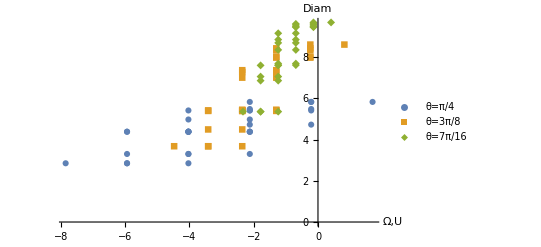

```mathematica
p=ListPlot[{WaterbombStripDiamTable5[π/4],WaterbombStripDiamTable5[3*π/8],WaterbombStripDiamTable5[7*π/16]},PlotLegends->{"θ=π/4","θ=3π/8","θ=7π/16"},AxesLabel->{"Ω,U","Diam"},PlotMarkers->Automatic]
```

```mathematica
Export["~/google-drive/Temp/2020-07-24/omega-vs-shape_N-5.pdf",p];
```

Export::nodir: Directory C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\ does not exist.

Export::noopen: Cannot open ~/google-drive/Temp/2020-07-24/omega-vs-shape_N-5.pdf.

```mathematica
N[WaterbombStripDiamTable5[angles[[1]]]]
```

Part::partd: Part specification angles⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression If[angles⟦1⟧≤π/2,2,1] cannot be used as a part specification.

ReplaceAll::reps: {{{ϕ1→ArcTan[Times[«3»]+Sin[«1»],-Cos[«1»] Plus[«2»]]},{ϕ1→ArcTan[Times[«2»]+Sin[«1»],Cos[«1»] Plus[«2»]]}}⟦If[angles⟦1⟧≤π/2,2,1]⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression If[angles⟦1⟧≤π/2,2,1] cannot be used as a part specification.

ReplaceAll::reps: {{{ϕ1→ArcTan[Times[«3»]+Sin[«1»],-Cos[«1»] Plus[«2»]]},{ϕ1→ArcTan[Times[«2»]+Sin[«1»],Cos[«1»] Plus[«2»]]}}⟦If[angles⟦1⟧≤π/2,2,1]⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression If[angles⟦1⟧≤π/2,2,1] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ReplaceAll::reps: {{{ϕ1→ArcTan[Times[«3»]+Sin[«1»],-Cos[«1»] Plus[«2»]]},{ϕ1→ArcTan[Times[«2»]+Sin[«1»],Cos[«1»] Plus[«2»]]}}⟦If[angles⟦1⟧≤π/2,2,1]⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{5. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+4. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+4. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+4. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+4. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{4. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+4. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{4. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{2. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+3. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{4. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{3. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+2. If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{4. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{4. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}]+If[angles⟦1⟧≤1.5708,ωA/.{θ→angles⟦1⟧},ωB/.{θ→angles⟦1⟧}],0.},{5. If[3.14159-1. angles⟦1⟧≤1.5708,ωA/.{θ→3.14159-1. angles⟦1⟧},ωB/.{θ→3.14159-1. angles⟦1⟧}],0.}}

```mathematica
angles={π/4,3*π/8,7*π/16};
labels={"piDiv4","3piDiv8","7piDiv16"};
For[i=1,i≤Length[angles],i++,
Print["~/google-drive/Temp/2020-07-24/wb_strip_" <> labels[[i]] <> ".csv",angles[[i]],i];
Export["~/google-drive/Temp/2020-07-24/wb_strip_" <> labels[[i]] <> ".csv", N[WaterbombStripDiamTable5[angles[[i]]]]];
]
```

~/google-drive/Temp/2020-07-24/wb_strip_piDiv4.csv π/4 1

Export::nodir: Directory C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\wb_strip_piDiv4.csv.

```mathematica
WaterbombStripDiamTable5D[θ_]:=Module[{ret,i,j,cases,case,Ω,d,N0,N1},
ret={};
cases=Flatten[Table[{a,b,c,d,e},{a,{True,False}},{b,{True,False}},{c,{True,False}},{d,{True,False}},{e,{True,False}}]];
For[i=1,i≤Length[cases]/5,i++,
case=Table[cases[[j]],{j,5*(i-1)+1,5*(i-1)+5}];
N0=Sum[If[case[[k]],0,1],{k,1,5}];
N1=Sum[If[case[[k]],1,0],{k,1,5}];
Ω=Sum[ω[If[case[[k]],θ,π-θ]],{k,1,5}];
d=WaterbombStripDiam[WaterbombStrip[θ,case]];
AppendTo[ret,{Ω,d,N0,N1}];
];
ret
];
```

```mathematica
Export["~/google-drive/Temp/2020-07-24/wb_strip_" <> labels[[1]] <> ".csv", N[WaterbombStripDiamTable5D[angles[[1]]]]]
Export["~/google-drive/Temp/2020-07-24/wb_strip_" <> labels[[2]] <> ".csv", N[WaterbombStripDiamTable5D[angles[[2]]]]]
Export["~/google-drive/Temp/2020-07-24/wb_strip_" <> labels[[3]] <> ".csv", N[WaterbombStripDiamTable5D[angles[[3]]]]]
```

Export::nodir: Directory C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\wb_strip_piDiv4.csv.

$Failed

Export::nodir: Directory C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\wb_strip_3piDiv8.csv.

$Failed

Export::nodir: Directory C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\grasinmj\Documents\~\google-drive\Temp\2020-07-24\wb_strip_7piDiv16.csv.

$Failed